# AntonAntonov/CryptocurrencyData

Cryptocurrency data retrieval

## Paclet Manifest

"Documentation"

"Diagrams"

"English"

"Guides"

"ReferencePages"

"Symbols"

"CryptocurrencyData.nb"DocumentationEnglishReferencePagesSymbolsCryptocurrencyData.nb

"Tutorials"

"Crypto-currenciesdataacquisitionwithvisualization.nb"DocumentationEnglishTutorialsCrypto-currenciesdataacquisitionwithvisualization.nb

"Cryptocurrenciesdataexplorations.nb"DocumentationEnglishTutorialsCryptocurrenciesdataexplorations.nb

"Kernel"

"CryptocurrencyData.wl"KernelCryptocurrencyData.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

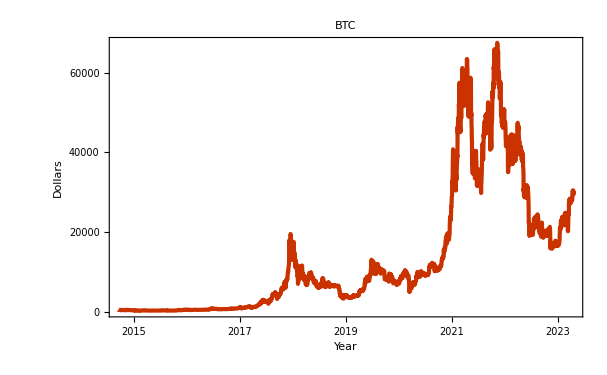

### Basic Description

Cryptocurrency data retrieval using function signatures very similar to FinancialData.

### Details

CryptocurencyData[name]

gives daily closing price data for the cryptocurrency name.

CryptocurencyData[name,start]

gives daily closing price data for the cryptocurrency name from start to current date.

CryptocurencyData[name,{start,end}]

gives daily closing price data for the cryptocurrency name from start to end.

CryptocurencyData[name,prop,{start,end}]

gives value of the specified property for the cryptocurrency name from start to end.

Generally speaking, CryptcurrencyData adheres to the signatures design of FinancialData, but there are a number of differences.

CryptocurrencyData utilizes two data sources: Yahoo Finance and data.bitcoinity.org.

CryptocurrencyData caches the source-retrived-and-processed data in order to provide results faster.

Here are the options taken:

Currency | USD | currency
LedgerStart | {2009, 1, 3} | ledger start date
Quantities | False | wether quantity units to be used or not
ResultType | TimeSeries | type of the result
Source | YahooFinance | source for cryptocurrency data

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`CryptocurrencyData`"];
```

### Basic Examples

Here is time series for Bitcoin (BTC):

```mathematica
CryptocurrencyData["BTC"]
```

TimeSeries[…]

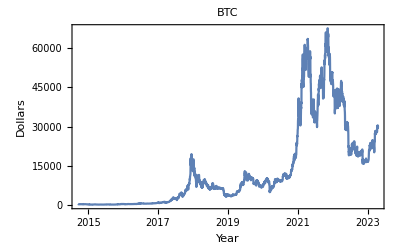

```mathematica
DateListPlot[%,]
```

Here is trading volume time series for BTC since 2018:

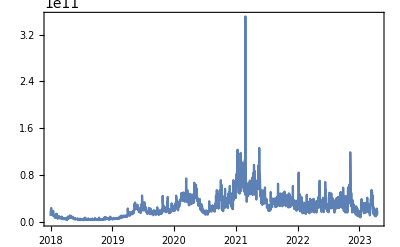

```mathematica
DateListPlot[CryptocurrencyData["BTC","Volume","Jan 1 2018"],PlotRange->All]
```

Get trading volume data for Bitcoin (BTC) and Ether (ETH) since January 1st 2022:

```mathematica
CryptocurrencyData[{"BTC","ETH"},"Volume","Jan 2022"]
```

<|BTC→TimeSeries[…],ETH→TimeSeries[…]|>

Here is the corresponding plot:

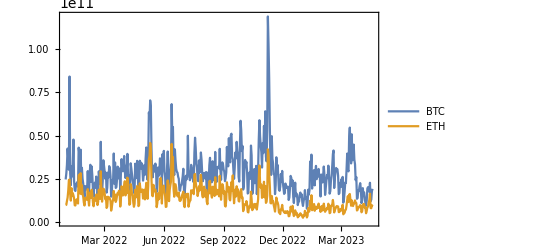

```mathematica
DateListPlot[%,PlotRange->All]
```

### Scope

Here are time series of different properties for Bitcoin (BTC) and Ether (ETH):

```mathematica
CryptocurrencyData[{"BTC","ETH"},{"Open","Volume"}]
```

<|BTC→<|Open→TimeSeries[…],Volume→TimeSeries[…]|>,ETH→<|Open→TimeSeries[…],Volume→TimeSeries[…]|>|>

Instead of time series we can get Dataset objects instead:

```mathematica
CryptocurrencyData[{"BTC","ETH"},{"Open","Volume"},"Jan 2021","ResultType"->Dataset]
```

-Graphics-

Get the cryptocurrency summary data from Yahoo Finance:

```mathematica
CryptocurrencyData[All,"Summary"]
```

-Graphics-

Get all classes of metadata and show the corresponding metadata values:

```mathematica
ResourceFunction["GridTableForm"][{#,CryptocurrencyData[#]}&/@CryptocurrencyData["Classes"],TableHeadings->{"Class","Values"}]
```

# | Class | Values
1 | Cryptocurrencies | {ADA,BCH,BNB,BTC,DOGE,DOT1,EOS,ETC,ETH,FIL,HEX,ICP1,LINK,LTC,MATIC,SOL1,THETA,TRX,UNI3,USDC,USDT,VET,XLM,XMR,XRP}
2 | Currencies | {AED,ARS,AUD,BRL,CAD,CHF,CLP,CNY,COP,CZK,DKK,EUR,GBP,HKD,HRK,HUF,IDR,ILS,INR,IRR,JPY,KES,KRW,MXN,MYR,NOK,NZD,PHP,PKR,PLN,RON,RUB,RUR,SAR,SEK,SGD,THB,TRY,UAH,USD,VEF,XAU,ZAR}
3 | Exchanges | {bit2c,bitbay,bitcoincentral,bitcoin.co.id,bitcoinde,bitcoinsnorway,bitcurex,bitfinex,bitflyer,bithumb,bitmarketpl,bitmex,bitquick,bitso,bitstamp,bit-x,btcchina,btce,btcmarkets,campbx,cex.io,clevercoin,coinbase,coinfloor,exmo,gemini,hitbtc,huobi,itbit,korbit,kraken,lakebtc,localbitcoins,mercadobitcoin,okcoin,paymium,quadrigacx,therocktrading,vaultoro,wallofcoins}

Get Bitcoin (BTC) data from the exchange "coinbase":

```mathematica
CryptocurrencyData[{"coinbase","BTC"},"Source"->"DataBitcoinityOrg"]
```

<|High→TimeSeries[…],Low→TimeSeries[…],Mean→TimeSeries[…]|>

Cryptocurrencies symbols and names:

```mathematica
CryptocurrencyData["CryptocurrencyNames"]
```

<|BTC→Bitcoin,ETH→Ethereum,USDT→Tether,BNB→BinanceCoin,ADA→Cardano,XRP→XRP,USDC→Coin,DOGE→Dogecoin,DOT1→Polkadot,HEX→HEX,UNI3→Uniswap,BCH→BitcoinCash,LTC→Litecoin,LINK→Chainlink,SOL1→Solana,MATIC→MaticNetwork,THETA→THETA,XLM→Stellar,VET→VeChain,ICP1→InternetComputer,ETC→EthereumClassic,TRX→TRON,FIL→FilecoinFutures,XMR→Monero,EOS→EOS|>

Currencies that can be used CryptocurrencyData:

```mathematica
CryptocurrencyData["Currencies"]
```

{AED,ARS,AUD,BRL,CAD,CHF,CLP,CNY,COP,CZK,DKK,EUR,GBP,HKD,HRK,HUF,IDR,ILS,INR,IRR,JPY,KES,KRW,MXN,MYR,NOK,NZD,PHP,PKR,PLN,RON,RUB,RUR,SAR,SEK,SGD,THB,TRY,UAH,USD,VEF,XAU,ZAR}

Exchanges that can be used in CryptocurrencyData with the option "Source" set to "DataBitcoinityOrg":

```mathematica
CryptocurrencyData["Exchanges"]
```

{bit2c,bitbay,bitcoincentral,bitcoin.co.id,bitcoinde,bitcoinsnorway,bitcurex,bitfinex,bitflyer,bithumb,bitmarketpl,bitmex,bitquick,bitso,bitstamp,bit-x,btcchina,btce,btcmarkets,campbx,cex.io,clevercoin,coinbase,coinfloor,exmo,gemini,hitbtc,huobi,itbit,korbit,kraken,lakebtc,localbitcoins,mercadobitcoin,okcoin,paymium,quadrigacx,therocktrading,vaultoro,wallofcoins}

### Options

#### Currency

The option "Currency" specifies the currency of the results. It is expected to be one of:

```mathematica
CryptocurrencyData["Currencies"]
```

{AED,ARS,AUD,BRL,CAD,CHF,CLP,CNY,COP,CZK,DKK,EUR,GBP,HKD,HRK,HUF,IDR,ILS,INR,IRR,JPY,KES,KRW,MXN,MYR,NOK,NZD,PHP,PKR,PLN,RON,RUB,RUR,SAR,SEK,SGD,THB,TRY,UAH,USD,VEF,XAU,ZAR}

Here are examples of opening prices of Ether (ETH) with different currencies:

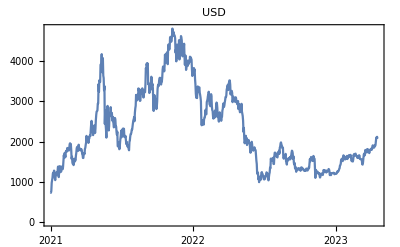
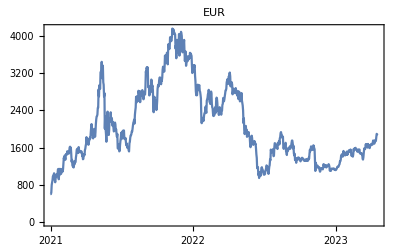
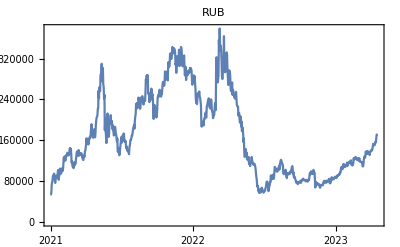

```mathematica
Table[DateListPlot[CryptocurrencyData["ETH","Open","Jan 1 2021","Currency"->c],PlotLabel->c],{c,{"USD","EUR","RUB"}}]
```

#### LedgerStart

The option "LedgerStart" specifies the start date of the cryptocurrency ledger. That start date is used when retrieval of all values is specified.

#### Quantities

If the option "ResultType" is set to TimeSeries, then the option "Quantities" specifies weather the result time series should be with numeric values with quantity values.

Here we obtain Ether opening price time series:

```mathematica
aRes=Association[#->CryptocurrencyData["ETH","Open",{"Jan 1, 2021","Jan, 7, 2021"},"ResultType"->TimeSeries,"Quantities"->#]&/@{True,False}]
```

<|True→TimeSeries[…],False→TimeSeries[…]|>

Here from each time series the values are extracted:

```mathematica
aRes2=Map[#["Values"]&,aRes]
```

<|True→QuantityArray[…],False→{737.708,730.403,774.512,977.059,1041.5,1101.01,1208.08}|>

QuantityArray is used in order to have faster data retrieval. After normalizing the results we see the actual quantities and values:

```mathematica
Map[Normal,aRes2]
```

<|True→{737.71 $,730.40 $,774.51 $,977.06 $,1 041.50 $,1 101.01 $,1 208.08 $},False→{737.708,730.403,774.512,977.059,1041.5,1101.01,1208.08}|>

Note that for trading volume the unit "Items" is used, since there is not unit "Coins":

```mathematica
Normal@CryptocurrencyData["ETH","Volume",{"Jan 1, 2021","Jan, 3, 2021"},"ResultType"->TimeSeries,"Quantities"->True]
```

{{3.81845×10^9,13652004358 items},{3.81853×10^9,19740771179 items},{3.81862×10^9,45200463368 items}}

#### ResultType

The option "ResultType" specifies the type of the results. It is expected to be Automatic, Dataset, or TimeSeries. Automatic is the same as TimeSeries. Here is are examples:

```mathematica
#->CryptocurrencyData["ETH","Close",{"Jan 1, 2021","Jan, 7, 2021"},"ResultType"->#]&/@{Automatic,Dataset,TimeSeries}
```

-Graphics-

#### Source

The option "Source" specifies the data source. It is expected to be Automatic, "YahooFinance", "YF", "DataBitcoinityOrg", or "DBO". The abbreviations "YF" and "DBO" correspond to the "YahooFinance" and "DataBitcoinityOrg" respectively. With "YahooFinance" data from the page https://finance.yahoo.com/cryptocurrencies is used. With "DataBitcoinityOrg" data from https://data.bitcoinity.org is used. Here are examples:

```mathematica
#->CryptocurrencyData["BTC","Close",{"Jan 1, 2021","Jan, 7, 2021"},"Source"->#]&/@{Automatic,"YahooFinance","DataBitcoinityOrg"}
```

{Automatic→TimeSeries[…],YahooFinance→TimeSeries[…],DataBitcoinityOrg→TimeSeries[…]}

### Applications

Find 100-day moving averages of a opening price of BTC:

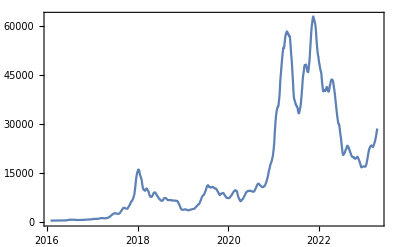

```mathematica
DateListPlot[MovingAverage[CryptocurrencyData["BTC","Open","Jan. 1, 2016"],30],PlotRange->All,PlotTheme->"Detailed"]
```

Find the summary of the opening price daily differences for BTC for the passed two years:

```mathematica
lsRes=CryptocurrencyData["BTC","Open",DatePlus[Now,-Quantity[2,"Years"]]]["Values"];
Row[{ResourceFunction["RecordsSummary"][Differences[lsRes],"Differences"],Spacer[5],ResourceFunction["RecordsSummary"][Log10/@Abs[Differences[lsRes]],"lg|differences|"]}]
```

{1 Differences
Min | -6979.1
1st Qu | -509.14
Mean | -36.6868
Median | -22.8242
3rd Qu | 523.502
Max | 5488.5}{1 lg|differences|
Min | 0.0681565
1st Qu | 2.30186
Mean | 2.64785
Median | 2.7166
3rd Qu | 3.05547
Max | 3.8438}

Plot a histogram of the corresponding to log 10 of the absolute values:

```mathematica
Histogram[Log10/@Abs[Differences[lsRes]],20,"Probability",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Log10 |USD|","Probability"}]
```

-Graphics-

Note the summary and plot above demonstrate the volatility of BTC.

Show the top eight "priciest" cryptocurrencies using data from the last two weeks:

```mathematica
aMeans=Select[Association[#->Mean[CryptocurrencyData[#,"Open",DatePlus[Now,-Quantity[2,"Weeks"]]]["Values"]]&/@CryptocurrencyData["Cryptocurrencies"]],NumberQ];
aTopMeans=Take[ReverseSort[aMeans],8]
```

<|BTC→29239.4,ETH→1953.67,BNB→322.046,XMR→160.135,BCH→128.79,LTC→93.881,ETC→21.42,LINK→7.49699|>

Plot the opening prices of top cryptocurrencies since 2018:

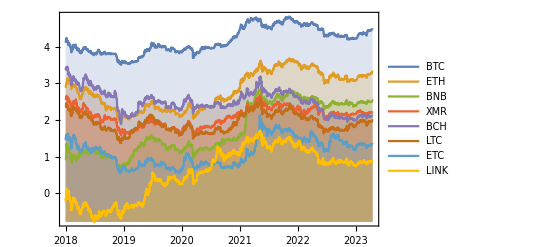

```mathematica
lsCCTop=Keys@aTopMeans;
DateListPlot[Log10/@Association[#->CryptocurrencyData[#,"Open","Jan 1, 2018"]&/@lsCCTop],Joined->True,Filling->Bottom,PlotRange->All]
```

### Properties and Relations

FinancialData has ten of the cryptocurrencies for which CryptocurrencyData can provide data for (through Yahoo Finance.) Here are the cryptocurrencies FinancialData knows the prices of:

```mathematica
Keys@Select[Association[#->FinancialData[#,"Jan. 1, 2021","Value"]&/@CryptocurrencyData["Cryptocurrencies"]],Head[#]=!=Missing&]
```

{ADA,BCH,EOS,ETC,ETH,FIL,HEX,LINK,LTC,TRX,USDC,VET,XLM}

Here is a time series for ETH:

```mathematica
FinancialData["ETH","Jan 1 2021"]
```

TimeSeries[…]

FinancialData does not provide cryptocurrency data other than price (e.g. trading volume, etc.) or data from different exchanges. Here are examples of a failed retrieval:

```mathematica
FinancialData["BTC","Volume","Jan 1 2021"]
```

Missing[NotAvailable]

Also, FinancialData returns cryptocurrency results without units. See comparison with stocks:

```mathematica
Table[a->ResourceFunction["RecordsSummary"][FinancialData[a,"Jan 1 2021"]["Values"]],{a,{"BTC","GE","APPL"}}]
```

{BTC→$Failed,GE→{1 column 1
104.72 $ | 4
104.96 $ | 4
102.08 $ | 3
103.60 $ | 3
105.04 $ | 3
105.20 $ | 3
(Other) | 555},APPL→$Failed}

Here is a 30 day moving average of the price of BTC with using FinancialData:

```mathematica
DateListPlot[MovingAverage[FinancialData["BTC","Jan. 1, 2018","Value"],30],{"Jan. 1, 2016",Automatic,"Day"},PlotRange->All,Joined->True]
```

DateListPlot[MovingAverage[Missing[NotAvailable],30],{Jan. 1, 2016,Automatic,Day},PlotRange→All,Joined→True]

Here is a 30 day moving average of the price of BTC with using CryptocurrencyData:

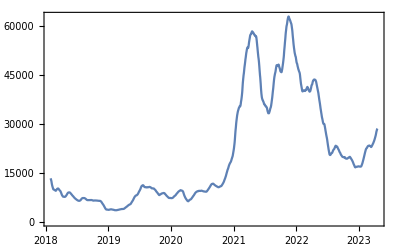

```mathematica
DateListPlot[MovingAverage[CryptocurrencyData["BTC","Open","Jan. 1, 2018"],30],{"Jan. 1, 2016",Automatic,"Day"},PlotRange->All,Joined->True]
```

### Neat Examples

Plot passed year opening prices and trading volumes of the top cryptocurrencies:

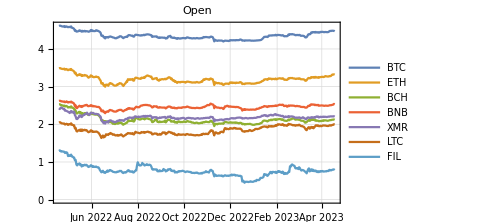
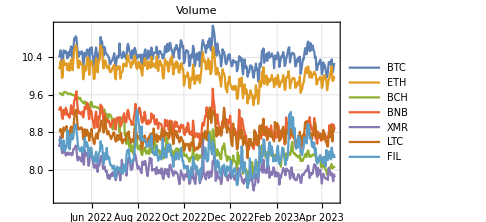

```mathematica
startDate=DatePlus[Now,-Quantity[1,"Years"]];
lsCCFocus={"BTC","ETH","BCH","BNB","XMR","LTC","FIL"};
lsPropFocus={"Open","Volume"};
Map[Function[{prop},DateListPlot[Log10/@Association[#->CryptocurrencyData[#,prop,startDate,"Currency"->"USD"]&/@lsCCFocus],PlotLabel->prop,ImageSize->Medium,PlotTheme->"Detailed"]],lsPropFocus]
```

Compute correlations between the passed year time series of the top cryptocurrencies:

```mathematica
startDate=DatePlus[Date[],-Quantity[1,"Years"]];
aRes=CryptocurrencyData[lsCCFocus,"Open",startDate,"ResultType"->TimeSeries];
aRes=Quiet[TimeSeriesResample[#,{startDate,Date[],Quantity[1,"Days"]}]&/@aRes];
matCor=Outer[{#1,#2,Correlation[aRes[#1]["Values"],aRes[#2]["Values"]]}&,Keys[aRes],Keys[aRes]];
dsCor=ResourceFunction["CrossTabulate"][Flatten[matCor,1]]
```

-Graphics-

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-CryptocurrencyData-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Cryptocurrency

Cryptocurrency data

Financial data

Time series

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Anton Antonov, "Crypto-currencies data acquisition with visualization", (2021), MathematicaForPrediction at WordPress.

Anton Antonov, "Cryptocurrencies data explorations", (2021), MathematicaForPrediction at WordPress.

### Links

All Cryptocurrencies Screener - Yahoo Finance

data.bitcoinity.org

### Compatibility

#### Wolfram Language Version

12.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.